```mathematica
Quit[];
```

#### Preamble

```mathematica
CC[x_]:=ColorConvert[x,"Grayscale"];
LD[x_,t_]:=If[t<0,Darker[x,-t],Lighter[x,t]];
CCLD[x_,t_]:=ColorConvert[If[t<0,Darker[x,-t],Lighter[x,t]],"GrayScale"];
QCS[x_]:=QuantityMagnitude[UnitConvert[x,"SIBase"]];
```

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
SetOptions[LogTicks,LogPlot->True];
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,physics}"}];
```

```mathematica
textStyle=Directive[FontSize-> 14,FontFamily->"Times New Roman"];
```

# Data and Plots

## Figure 4: Plot of G(α)

```mathematica
funcG[α_]:=NIntegrate[((1+Erf[x/(√2)])/2)^(2α-2)*Exp[-x^2],{x,-∞,+∞}];
```

```mathematica
tab=Table[{α,funcG[α]},{α,0.5,2,0.01}];
```

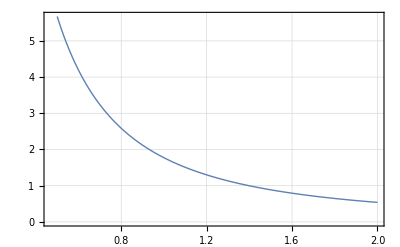

```mathematica
funcGplot=ListLinePlot[tab,
PlotRange->All,
PlotStyle->{Thick},
Frame->True,
FrameStyle->BlackFrame,
GridLines->Automatic,
FrameLabel->MaTeX[{"\\alpha","G(\\alpha)"},Magnification->1.2]]
```

```mathematica
(*Export["funcGplot.pdf",funcGplot];*)
```

## Figure 5: Graphene Disk Localization

```mathematica
rA=10^-10;rD=10^-5;mA=12;mRCnt=1;nA=10^10;
mD=nA*mA;
```

```mathematica
n[rC_]:=Piecewise[{{1,rC<rA},{(rC/rA)^2,rA<rC<rD},{nA,rC>rD}}];
```

```mathematica
λLowerBound[rC_,τ_,d_,α_]:=(nA/n[rC]((mA*n[rC])/mRCnt)^(2α)τ*(1-Exp[(-α d^2)/(4 rC^2)]))^-1;
```

```mathematica
λThinDiskSophisticatedBoundOLD[rC_,τ_,d_,α_]:=1/τ*(((π*rC^2)/α)^(3/2)*1/((2π rC^2)^(3α)))*(1/2*(mD/mRCnt*2/((2π)^(3/2)*rC*rD))^(2α)*(√π rC)/(√α)*(2 rD^2)/rD^(2α)*(π-2(ArcSin[√(1-(d/(2*rD))^2)]-d/(2*rD)√(1-(d/(2*rD))^2))))^-1;
```

```mathematica
λThinDiskSophisticatedBound[rC_,τ_,d_,α_]:=(τ*α/π*((2mD)/mRCnt)^(2α)*(rC/rD)^(4α-2)*(π-2(ArcSin[√(1-(d/(2*rD))^2)]-d/(2*rD)√(1-(d/(2*rD))^2))))^-1;
```

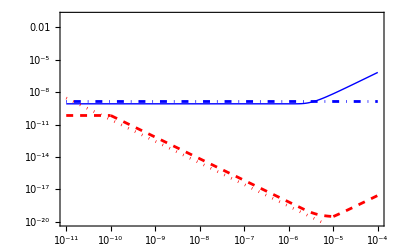

```mathematica
theoryboundPlotOne=Quiet[LogLogPlot[{λLowerBound[rC,10^-2,rD,1/2],λLowerBound[rC,10^-2,rD,1],λThinDiskSophisticatedBound[rC,10^-2,rD,1/2],λThinDiskSophisticatedBound[rC,10^-2,rD,1]},{rC,10^-11,10^-4},
PlotRange->{10^-20,10^-1},
PlotStyle->{{Thick,Blue},{Dashed,Red},{DotDashed,Blue},{Dotted,Red}},
Frame->True,
ImageSize->400,
FrameStyle->Directive[BlackFrame,15],
GridLines->Automatic,
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_\\alpha [\\rm{s}^{-1}]"},Magnification->1.8],
PlotLegends->Placed[LineLegend[MaTeX[{"\\lambda_{1/2}\\vert_{\\rm Adler}","\\lambda_{1}\\vert_{\\rm Adler}","\\lambda_{1/2}\\vert_{r_C \\ll r_D}","\\lambda_{1}\\vert_{r_C \\ll r_D}"},Magnification->1.5],LegendFunction->(Framed[#,FrameMargins->0,Background->White,RoundingRadius->6,FrameStyle->BlackFrame]&),LegendLayout->{"Row",2}],Scaled[{0.38,0.80}]]]]
```

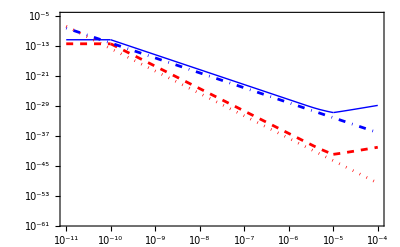

```mathematica
theoryboundPlotTwo=Quiet[LogLogPlot[{λLowerBound[rC,10^-2,rD,3/2],λLowerBound[rC,10^-2,rD,2],λThinDiskSophisticatedBound[rC,10^-2,rD,3/2],λThinDiskSophisticatedBound[rC,10^-2,rD,2]},{rC,10^-11,10^-4},
PlotRange->{10^-60,10^-5},
PlotStyle->{{Thick,Blue},{Dashed,Red},{DotDashed,Blue},{Dotted,Red}},
Frame->True,
ImageSize->400,
FrameStyle->Directive[BlackFrame,15],
GridLines->Automatic,
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_\\alpha [\\rm{s}^{-1}]"},Magnification->1.8],
PlotLegends->Placed[LineLegend[MaTeX[{"\\lambda_{3/2}\\vert_{\\rm Adler}","\\lambda_{2}\\vert_{\\rm Adler}","\\lambda_{3/2}\\vert_{r_C \\ll r_D}","\\lambda_{2}\\vert_{r_C \\ll r_D}"},Magnification->1.5],LegendFunction->(Framed[#,FrameMargins->0,Background->White,RoundingRadius->6,FrameStyle->BlackFrame]&),LegendLayout->{"Row",2}],Scaled[{0.38,0.19}]]]]
```

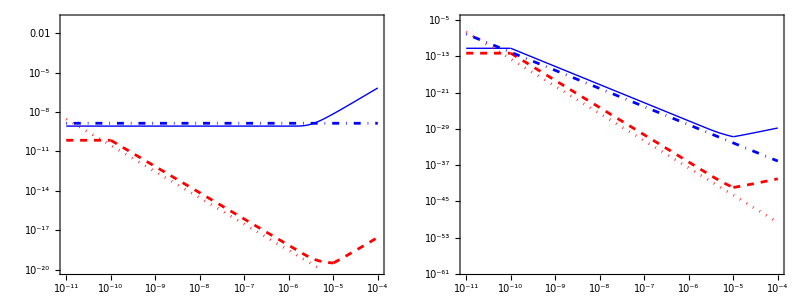

```mathematica
theoryboundPlots=Grid[{{theoryboundPlotOne,theoryboundPlotTwo}},Spacings->{2,{0,-0.1,1}}]
```

```mathematica
(*Export["theoryboundPlots.pdf",theoryboundPlots];*)
```

## Figure 6: Comparison with PRD 94, 124036 (2016)

## Functions from PRD 94, 124036 (2016)

```mathematica
fCorr[rC_,a_,L_]:=1/2 Exp[-(a+L)^2/(4 rC^2)](1+Exp[(a L)/rC^2]-2Exp[(L(2a+L))/(4 rC^2)]);
```

```mathematica
SLigo[rC_,a_,L_,R_,λ_,MC_,mR_]:=(8 ℏ^2 λ MC^2)/(L^2 mR^2)(rC/R)^2(1-Exp[-L^2/(4 rC^2)]+fCorr[rC,a,L])*(1-Exp[-R^2/(2 rC^2)](BesselI[0,R^2/(2 rC^2)]+BesselI[1,R^2/(2 rC^2)]));
```

```mathematica
SLisa[rC_,a_,L_,λ_,MC_,mR_]:=(16 ℏ^2 λ MC^2)/(L^2 mR^2)(rC/L)^4(1-Exp[-L^2/(4 rC^2)]+fCorr[rC,a,L])*(1-Exp[-L^2/(4 rC^2)]-√π L/(2rC)Erf[L/(2rC)])^2;
```

```mathematica
ℏ=Quantity[1,"ReducedPlanckConstant"];
mRPhys=Quantity[1,"ProtonMass"];
```

```mathematica
MCLigo=Quantity[40,"Kilograms"];
aLigo=Quantity[4,"Kilometers"];
LLigo=Quantity[20,"Centimeters"];
RLigo=Quantity[17,"Centimeters"];
```

```mathematica
MCLisa=Quantity[1.928,"Kilograms"];
aLisa=Quantity[37.6,"Centimeters"];
LLisa=Quantity[4.6,"Centimeters"];
```

```mathematica
SLigoMeas=UnitConvert[Quantity[(9.5*10^-14)^2,("Newtons")^2*"Seconds"],"SIBase"];
SLisaMeas=UnitConvert[MCLisa^2/4 Quantity[2.7*10^-29,("Meters")^2*("Seconds")^-3],"SIBase"];
```

```mathematica
λLigo[rC_]:=SLigoMeas*(2*(8 ℏ^2 MCLigo^2)/(LLigo^2 mRPhys^2)(rC/RLigo)^2(1-Exp[-LLigo^2/(4 rC^2)]+fCorr[rC,aLigo,LLigo])*(1-Exp[-RLigo^2/(2 rC^2)](BesselI[0,RLigo^2/(2 rC^2)]+BesselI[1,RLigo^2/(2 rC^2)])))^-1;(*In the paper they say to multiply again by two because of the two arms of Ligo*)
```

```mathematica
λLisa[rC_]:=SLisaMeas*(2*(16 ℏ^2 MCLisa^2)/(LLisa^2 mRPhys^2)(rC/LLisa)^4(1-Exp[-LLisa^2/(4 rC^2)]+fCorr[rC,aLisa,LLisa])*(1-Exp[-LLisa^2/(4 rC^2)]-√π LLisa/(2rC)Erf[LLisa/(2rC)])^2)^-1;
```

## Functions from Piccione_PRA

```mathematica
funcG[α_]:=NIntegrate[((1+Erf[x/(√2)])/2)^(2α-2)*Exp[-x^2],{x,-∞,+∞}];
```

```mathematica
SsmallRC[α_,rC_,L_,A_,λ_,M_,mR_]:=λ*ℏ^2/2*(M/mR)^(2α)*(α^(7/2)A funcG[α](2π rC^2)^(3α))/((L*A)^(2α)π^(5/2)rC^4);
```

```mathematica
SlargeRCOLD[α_,rC_,a_,λ_,MC_,mR_]:=λ*(α ℏ^2)/(4 rC^2)(MC/mR)^(2α)( 1 +((α*a^2)/(2 rC^2)- 1 )ⅇ^(-(a^2 α)/(4 rC^2)));
```

```mathematica
fSNumeric[a_,α_]:=NIntegrate[(ⅇ^(-x^2/2)+ⅇ^(-(x+a)^2/2))^(2α-2)(x*ⅇ^(-x^2/2)-(x+a)*ⅇ^(-(x+a)^2/2))^2,{x,-∞,+∞},Method->"MultiPeriodic"];(*For some reasons this does not work well and gives, sometimes, a result wrong by a factor 2*)
fS1s2[a_]:=2 √(2π)(1-ⅇ^(-a^2/2));
fS1[a_]:=√π(1+(1/2 a^2-1)ⅇ^(-a^2/4));
fS3s2[a_]:=2/3 √((2 π)/3)(1+(5/3 a^2-1)ⅇ^(-a^2/3));
fS2[a_]:=1/2 √(π/2)(1+(3 a^2-1)ⅇ^(-a^2/2)+2 a^2 ⅇ^(-(3 a^2)/8));
fS[a_,α_]:={fS1s2[a],fS1[a],fS3s2[a],fS2[a]}[[2α]];
SlargeRC[α_,rC_,a_,λ_,MC_,mR_]:=λ*(α^(5/2) ℏ^2)/(4 √π rC^2)(MC/mR)^(2α)fS[a/rC,α];
```

```mathematica
λSmallRCLigo[α_,rC_,multExpNoise_]:=multExpNoise*SLigoMeas*(4*ℏ^2/2*(MCLigo/mRPhys)^(2α)*(α^(7/2)π*RLigo^2 funcG[α](2π rC^2)^(3α))/((LLigo*π*RLigo^2)^(2α)π^(5/2)rC^4))^-1;
λLargeRCLigoOLD[α_,rC_,multExpNoise_]:=multExpNoise*SLigoMeas*(4*(α ℏ^2)/(4 rC^2)(MCLigo/mRPhys)^(2α)( 1 +((α*aLigo^2)/(2 rC^2)- 1 )ⅇ^(-(aLigo^2 α)/(4 rC^2))))^-1;
λLargeRCLigo[α_,rC_,multExpNoise_]:=Module[{k=aLigo/rC,fSN},fSN=fS[k,α];Return[multExpNoise*SLigoMeas*(4*(α^(5/2) ℏ^2)/(4 √π rC^2)(MCLigo/mRPhys)^(2α)fSN)^-1]];(*Multiplication by 4 because: twice for one-sided spectrum and twice because two arms in Ligo.*)
```

```mathematica
λSmallRCLisa[α_,rC_,multExpNoise_]:=multExpNoise*SLisaMeas*(2*ℏ^2/2*(MCLisa/mRPhys)^(2α)*(α^(7/2)LLisa^2 funcG[α](2π rC^2)^(3α))/((LLisa*LLisa^2)^(2α)π^(5/2)rC^4))^-1;
λLargeRCLisaOLD[α_,rC_,multExpNoise_]:=multExpNoise*SLisaMeas*(2*(α ℏ^2)/(4 rC^2)(MCLisa/mRPhys)^(2α)( 1 +((α*aLisa^2)/(2 rC^2)- 1 )ⅇ^(-(aLisa^2 α)/(4 rC^2))))^-1;
λLargeRCLisa[α_,rC_,multExpNoise_]:=Module[{k=aLisa/rC,fSN},fSN=fS[k,α];Return[multExpNoise*SLisaMeas*(2*(α^(5/2) ℏ^2)/(4 √π rC^2)(MCLisa/mRPhys)^(2α)fSN)^-1]];
(*Multiplication by 2 because one-sided spectrum.*)
```

```mathematica
λRCLigo[α_,rC_,multExpNoise_]:=Max[λSmallRCLigo[α,rC,multExpNoise],λLargeRCLigo[α,rC,multExpNoise]];
λRCLisa[α_,rC_,multExpNoise_]:=Max[λSmallRCLisa[α,rC,multExpNoise],λLargeRCLisa[α,rC,multExpNoise]];
```

## Plots

```mathematica
tabRC=Table[10^x,{x,-11,2,0.1}];
tabLigo=Quiet[Table[{rC,λLigo[Quantity[rC,"Meters"]]/Quantity[1,"Hertz"]},{rC,tabRC}]];
tabLisa=Quiet[Table[{rC,λLisa[Quantity[rC,"Meters"]]/Quantity[1,"Hertz"]},{rC,tabRC}]];
```

```mathematica
tabNPOneRCLigo=Quiet[Table[{rC,λRCLigo[1,Quantity[rC,"Meters"],1]/Quantity[1,"Hertz"]},{rC,tabRC}]];
```

```mathematica
tabNPOneRCLisa=Quiet[Table[{rC,λRCLisa[1,Quantity[rC,"Meters"],1]/Quantity[1,"Hertz"]},{rC,tabRC}]];
```

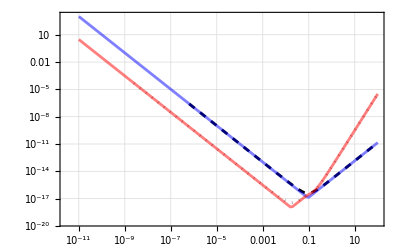

```mathematica
comparisonPlotGravWaves=ListLogLogPlot[{tabLigo,tabNPOneRCLigo,tabLisa,tabNPOneRCLisa},
PlotLegends->MaTeX[{"\\textrm{LIGO [from PRD \\textbf{94}, 124036]}","\\textrm{LIGO [from Eq. (E19)]}","\\textrm{LISA Pathfinder [from PRD \\textbf{94}, 124036]}","\\textrm{LISA Pathfinder [from Eq. (E19)]}"},Magnification->1.1],
PlotStyle->{{Dashed,Black},{Thick,Blue,Opacity[0.5]},{Dotted,Gray},{Thick,Red,Opacity[0.5]}},
Joined->True,
Frame->True,
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_1 (r_C) [\\rm{s}^{-1}]"},Magnification->1.4],
FrameStyle->Directive[BlackFrame,13],
GridLines->Automatic]
```

```mathematica
(*Export["comparisonPlotGravWaves.svg",comparisonPlotGravWaves];*)
```

```mathematica
(*Export["comparisonPlotGravWaves.pdf",comparisonPlotGravWaves];*)
```

## Spontaneous Radiation formulas

```mathematica
mRPhys=Quantity[1,"ProtonMass"];
UnitGermDetMass=Quantity[44.1,"Kilograms"];
GermDensity=Quantity[5327,"Kilograms"*("Meters")^-3];
```

```mathematica
EmissαFormula=(α^(7/2)*λα*Q^2*ℏ*(2π rC^2)^(3α)μ0^(2α-2))/(32 π^5 ϵ0 c^3 mR^(2α)rC^8 ω);
```

```mathematica
Emiss1Formula=(Q^2 λα ℏ)/(4 c^3 mR^2 π^2 rC^2 ϵ0 ω);
```

```mathematica
FullSimplify[EmissαFormula/Emiss1Formula]
```

(mR^(2-2 α) (2 π)^(3 (-1+α)) (rC^2)^(3 α) α^(7/2) μ0^(-2+2 α))/rC^6

```mathematica
λαSpontRadSmallRC[α_,rC_,multExpNoise_]:=Module[{mR=QCS[mRPhys],μ0=QCS[GermDensity]},rC^2*((mR^(2-2 α) (2 π)^(3 (-1+α)) (rC^2)^(3 α) α^(7/2) μ0^(-2+2 α))/rC^6)^-1*multExpNoise*4.79*10^-1];
```

```mathematica
λαSpontRadLargeRC[α_,rC_,multExpNoise_]:=Module[{mR=QCS[mRPhys],M=QCS[UnitGermDetMass]},rC^2*(α*(M/mR)^(2α-2))^-1*multExpNoise*4.79*10^-1];
```

```mathematica
λαSpontRad[α_,rC_,multExpNoise_]:=If[α<=1,Min[λαSpontRadSmallRC[α,rC,multExpNoise],λαSpontRadLargeRC[α,rC,multExpNoise]],Max[λαSpontRadSmallRC[α,rC,multExpNoise],λαSpontRadLargeRC[α,rC,multExpNoise]]];
```

## Exclusion plots [Figures 1 and 3]

## Tables

```mathematica
ImSz=400;numDim=15;plLblMag=1.6;FrLbl=1.5;
```

```mathematica
tabRC=Table[10^x,{x,-11,2,0.1}];
```

```mathematica
tabRC2=Table[10^x,{x,-11,2,0.01}];
```

```mathematica
tabLowerBoundOneHalf=Quiet[Table[{rC,λLowerBound[rC,10^-2,rD,1/2]},{rC,tabRC2}]];
tabLowerBoundOne=Quiet[Table[{rC,λLowerBound[rC,10^-2,rD,1]},{rC,tabRC2}]];
tabLowerBoundThreeHalf=Quiet[Table[{rC,λLowerBound[rC,10^-2,rD,3/2]},{rC,tabRC2}]];
tabLowerBoundTwo=Quiet[Table[{rC,λLowerBound[rC,10^-2,rD,2]},{rC,tabRC2}]];
```

```mathematica
tabRadiationBoundOneHalf=Quiet[Table[{rC,λαSpontRad[1/2,rC,1]},{rC,tabRC2}]];
tabRadiationBoundOne=Quiet[Table[{rC,λαSpontRad[1,rC,1]},{rC,tabRC2}]];
tabRadiationBoundThreeHalf=Quiet[Table[{rC,λαSpontRad[3/2,rC,1]},{rC,tabRC2}]];
tabRadiationBoundTwo=Quiet[Table[{rC,λαSpontRad[2,rC,1]},{rC,tabRC2}]];
```

```mathematica
tabNPAlphaRCLigo=Quiet[Table[Table[{rC,λRCLigo[α,Quantity[rC,"Meters"],1]/Quantity[1,"Hertz"]},{rC,tabRC}],{α,1/2,2,1/2}]];
tabNPAlphaRCLisa=Quiet[Table[Table[{rC,λRCLisa[α,Quantity[rC,"Meters"],1]/Quantity[1,"Hertz"]},{rC,tabRC}],{α,1/2,2,1/2}]];
```

```mathematica
tabRadiationBoundOneHalfMultExpRad=Quiet[Table[{rC,λαSpontRad[1/2,rC,6*10^-10]},{rC,tabRC2}]];
```

```mathematica
tabNPOneHalfRCLisaMultExpGrav=Quiet[Table[{rC,λRCLisa[1/2,Quantity[rC,"Meters"],2.2*10^-9]/Quantity[1,"Hertz"]},{rC,tabRC}]];
```

```mathematica
tabNPOneHalfRCLigoMultExpGrav=Quiet[Table[{rC,λRCLigo[1/2,Quantity[rC,"Meters"],6*10^-12]/Quantity[1,"Hertz"]},{rC,tabRC}]];
```

## Preparation Exclusion Plot with real data [Figure 1]

```mathematica
exclusionPlotOneHalf=ListLogLogPlot[{tabNPAlphaRCLigo[[2*1/2]],tabNPAlphaRCLisa[[2*1/2]],tabRadiationBoundOneHalf,tabLowerBoundOneHalf},
Joined->True,
PlotStyle->{{Red,Dotted},{Green,DotDashed},{Blue,Dashed},{Gray,Thick}},
PlotRange->{{10^-10,10^2},{10^-10,10^18}},
Epilog-> Inset[Framed[MaTeX["\\alpha=1/2",Magnification->plLblMag],RoundingRadius->6,Background->White],Scaled[{0.15,0.9}]],
Filling->{1->Top,2->Top,3->Top,4->Bottom},
Frame->True,
ImageSize->ImSz,
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_{1/2} (r_C)[\\rm{s}^{-1}]"},Magnification->FrLbl],
FrameStyle->Directive[BlackFrame,numDim],
FrameTicks->{{LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False]]},{LogTicks[10^-10,10^2,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^2,TickLabelStep->2,ShowMinorTicks->False]]}},
GridLines->{Table[10^x,{x,-9,1,2}],Table[10^x,{x,-9,15,4}]}]
```

-Graphics-

```mathematica
exclusionPlotOne=ListLogLogPlot[{tabNPAlphaRCLigo[[2*1]],tabNPAlphaRCLisa[[2*1]],tabRadiationBoundOne,tabLowerBoundOne},
ImageSize->ImSz,
Joined->True,
PlotStyle->{{Red,Dotted},{Green,DotDashed},{Blue,Dashed},{Gray,Thick}},
Frame->True,
PlotRange->{{10^-10,10^2},{10^-20,10^-8}},
Epilog-> Inset[Framed[MaTeX["\\alpha=1",Magnification->plLblMag],RoundingRadius->6,Background->White],Scaled[{0.15,0.9}]],
Filling->{1->Top,2->Top,3->Top,4->Bottom},
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_{1} (r_C)[\\rm{s}^{-1}]"},Magnification->FrLbl],
FrameStyle->Directive[BlackFrame,numDim],
FrameTicks->{{LogTicks[10^-20,10^-8,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-20,10^-8,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False]]},{LogTicks[10^-10,10^2,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^2,TickLabelStep->2,ShowMinorTicks->False]]}},
GridLines->{Table[10^x,{x,-9,1,2}],Table[10^x,{x,-19,-9,2}]}]
```

-Graphics-

```mathematica
exclusionPlotThreeHalf=ListLogLogPlot[{tabNPAlphaRCLigo[[2*3/2]],tabNPAlphaRCLisa[[2*3/2]],tabRadiationBoundThreeHalf,tabLowerBoundThreeHalf},
ImageSize->ImSz,
Joined->True,
PlotStyle->{{Red,Dotted},{Green,DotDashed},{Blue,Dashed},{Gray,Thick}},
Frame->True,
PlotRange->{{10^-10,10^2},{10^-32,10^-25}},
Epilog-> Inset[Framed[MaTeX["\\alpha=3/2",Magnification->plLblMag],RoundingRadius->6,Background->White],Scaled[{0.15,0.2}]],
Filling->{1->Top,2->Top,3->Top,4->Bottom},
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_{3/2} (r_C)[\\rm{s}^{-1}]"},Magnification->FrLbl],
FrameStyle->Directive[BlackFrame,numDim],
FrameTicks->{{LogTicks[10^-32,10^-25,TickLabelStep->1,TickLabelStart->0,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-32,10^-25,TickLabelStep->1,TickLabelStart->0,ShowMinorTicks->False]]},{LogTicks[10^-10,10^2,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^2,TickLabelStep->2,ShowMinorTicks->False]]}},
GridLines->{Table[10^x,{x,-9,1,2}],Table[10^x,{x,-32,-25,1}]}]
```

-Graphics-

```mathematica
exclusionPlotTwo=ListLogLogPlot[{tabNPAlphaRCLigo[[2*2]],tabNPAlphaRCLisa[[2*2]],tabRadiationBoundTwo,tabLowerBoundTwo},
ImageSize->ImSz,
Joined->True,
PlotStyle->{{Red,Dotted},{Green,DotDashed},{Blue,Dashed},{Gray,Thick}},
Frame->True,
PlotRange->{{10^-10,10^2},{10^-70,10^-0}},
Epilog-> Inset[Framed[MaTeX["\\alpha=2",Magnification->plLblMag],RoundingRadius->6,Background->White],Scaled[{0.15,0.2}]],
Filling->{1->Top,2->Top,3->Top,4->Bottom},
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_{2} (r_C)[\\rm{s}^{-1}]"},Magnification->FrLbl],
FrameStyle->Directive[BlackFrame,numDim],
FrameTicks->{{LogTicks[10^-70,10^-0,TickLabelStep->10,TickLabelStart->0,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-70,10^-0,TickLabelStep->10,TickLabelStart->0,ShowMinorTicks->False]]},{LogTicks[10^-10,10^2,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^2,TickLabelStep->2,ShowMinorTicks->False]]}},
GridLines->{Table[10^x,{x,-9,1,2}],Table[10^x,{x,-70,-0,10}]}]
```

-Graphics-

## Final Plot Figure 1

```mathematica
exclusionPlotsV2=Grid[{{exclusionPlotOneHalf,exclusionPlotOne},{exclusionPlotThreeHalf,exclusionPlotTwo}},Spacings->{2,{0,-0.1,1}}]
```

-Graphics-

```mathematica
(*Export["exclusionPlotsV2.pdf",exclusionPlotsV2];*)
```

## Preparation Exclusion Plots with Augmented Experimental Capabilities [Figure 3], alpha = 1/2

```mathematica
exclusionPlotOneHalf=ListLogLogPlot[{tabNPAlphaRCLigo[[2*1/2]],tabNPAlphaRCLisa[[2*1/2]],tabRadiationBoundOneHalf,tabLowerBoundOneHalf},
Joined->True,
PlotStyle->{{Red,Dotted},{Green,DotDashed},{Blue,Dashed},{Gray,Thick}},
PlotRange->{{10^-10,10^2},{10^-10,10^18}},
Epilog-> Inset[Framed[MaTeX["\\alpha=1/2",Magnification->plLblMag],RoundingRadius->6,Background->White],Scaled[{0.15,0.9}]],
Filling->{1->Top,2->Top,3->Top,4->Bottom},
Frame->True,
ImageSize->ImSz,
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_{1/2} (r_C)[\\rm{s}^{-1}]"},Magnification->FrLbl],
FrameStyle->Directive[BlackFrame,numDim],
FrameTicks->{{LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False]]},{LogTicks[10^-10,10^2,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^2,TickLabelStep->2,ShowMinorTicks->False]]}},
GridLines->{Table[10^x,{x,-9,1,2}],Table[10^x,{x,-9,15,4}]}]
```

-Graphics-

```mathematica
exclusionPlotOneHalfMultExpRad=ListLogLogPlot[{tabNPAlphaRCLigo[[2*1/2]],tabNPAlphaRCLisa[[2*1/2]],tabRadiationBoundOneHalfMultExpRad,tabLowerBoundOneHalf},
Joined->True,
PlotStyle->{{Red,Dotted},{Green,DotDashed},{Blue,Dashed},{Gray,Thick}},
PlotRange->{{10^-10,10^2},{10^-10,10^18}},
Epilog-> Inset[Framed[MaTeX["\\left[\\frac{\\dd{\\Gamma}}{\\dd{E}}\\right]\\Bigg\\vert_{\\rm Exp}\\rightarrow 6\\times 10^{-6}\\left[\\frac{\\dd{\\Gamma}}{\\dd{E}}\\right]\\Bigg\\vert_{\\rm Exp}",Magnification->0.7*plLblMag],RoundingRadius->6,Background->White],Scaled[{0.3,0.85}]],
Filling->{1->Top,2->Top,3->Top,4->Bottom},
Frame->True,
ImageSize->ImSz,
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_{1/2} (r_C)[\\rm{s}^{-1}]"},Magnification->FrLbl],
FrameStyle->Directive[BlackFrame,numDim],
FrameTicks->{{LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False]]},{LogTicks[10^-10,10^2,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^2,TickLabelStep->2,ShowMinorTicks->False]]}},
GridLines->{Table[10^x,{x,-9,1,2}],Table[10^x,{x,-9,15,4}]}]
```

-Graphics-

```mathematica
exclusionPlotOneHalfMultExpGravLISA=ListLogLogPlot[{tabNPAlphaRCLigo[[2*1/2]],tabNPOneHalfRCLisaMultExpGrav,tabRadiationBoundOneHalf,tabLowerBoundOneHalf},
Joined->True,
PlotStyle->{{Red,Dotted},{Green,DotDashed},{Blue,Dashed},{Gray,Thick}},
PlotRange->{{10^-10,10^2},{10^-10,10^18}},
Epilog-> Inset[Framed[MaTeX["S\\vert_{\\rm Exp}^{\\rm LISA}\\rightarrow 2.2\\times 10^{-9} S\\vert_{\\rm Exp}^{\\rm LISA}",Magnification->0.7*plLblMag],RoundingRadius->6,Background->White],Scaled[{0.25,0.9}]],
Filling->{1->Top,2->Top,3->Top,4->Bottom},
Frame->True,
ImageSize->ImSz,
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_{1/2} (r_C)[\\rm{s}^{-1}]"},Magnification->FrLbl],
FrameStyle->Directive[BlackFrame,numDim],
FrameTicks->{{LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False]]},{LogTicks[10^-10,10^2,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^2,TickLabelStep->2,ShowMinorTicks->False]]}},
GridLines->{Table[10^x,{x,-9,1,2}],Table[10^x,{x,-9,15,4}]}]
```

-Graphics-

```mathematica
exclusionPlotOneHalfMultExpGravLIGO=ListLogLogPlot[{tabNPOneHalfRCLigoMultExpGrav,tabNPAlphaRCLisa[[2*1/2]],tabRadiationBoundOneHalf,tabLowerBoundOneHalf},
Joined->True,
PlotStyle->{{Red,Dotted},{Green,DotDashed},{Blue,Dashed},{Gray,Thick}},
PlotRange->{{10^-10,10^2},{10^-10,10^18}},
Epilog-> Inset[Framed[MaTeX["S\\vert_{\\rm Exp}^{\\rm LIGO}\\rightarrow 6\\times 10^{-12} S\\vert_{\\rm Exp}^{\\rm LIGO}",Magnification->0.7*plLblMag],RoundingRadius->6,Background->White],Scaled[{0.25,0.9}]],
Filling->{1->Top,2->Top,3->Top,4->Bottom},
Frame->True,
ImageSize->ImSz,
FrameLabel->MaTeX[{"r_C [\\rm{m}]","\\lambda_{1/2} (r_C)[\\rm{s}^{-1}]"},Magnification->FrLbl],
FrameStyle->Directive[BlackFrame,numDim],
FrameTicks->{{LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^18,TickLabelStep->4,TickLabelStart->1,ShowMinorTicks->False]]},{LogTicks[10^-10,10^2,TickLabelStep->2,TickLabelStart->1,ShowMinorTicks->False],StripTickLabels[LogTicks[10^-10,10^2,TickLabelStep->2,ShowMinorTicks->False]]}},
GridLines->{Table[10^x,{x,-9,1,2}],Table[10^x,{x,-9,15,4}]}]
```

-Graphics-

## Final Plot Figure 3

```mathematica
exclusionPlotOneHalfModExp=Grid[{{exclusionPlotOneHalf,exclusionPlotOneHalfMultExpRad},{exclusionPlotOneHalfMultExpGravLISA,exclusionPlotOneHalfMultExpGravLIGO}},Spacings->{2,{0,-0.1,1}}]
```

-Graphics-

```mathematica
(*Export["exclusionPlotOneHalfModExp.pdf",exclusionPlotOneHalfModExp];*)
```